```mathematica
Clear[f0]
Clear[α]
```

```mathematica
cM=f0*2*Pi/allZeros[[1]][[3]];
```

```mathematica
Λ=Pi*acyl*acyl*(Sum[Integrate[r*Sin[allZeros[[l]][[1]]*(ϕ-β)]*BesselJ[allZeros[[l]][[1]],allZeros[[l]][[3]]*r],{r,0,atymp},{ϕ,β,2*Pi-β}]^2/(ρm*d*(ω^2-2*I*α*ω-cM^2*allZeros[[l]][[3]]^2)*Integrate[r*Sin[allZeros[[l]][[1]]*(ϕ-β)]^2*BesselJ[allZeros[[l]][[1]],allZeros[[l]][[3]]*r]^2,{r,0,atymp},{ϕ,β,2*Pi-β}]),{l,1,1}])^-1;
```

```mathematica
Λ
```

(0.125517+0. ⅈ) (-39.4784 f0^2+4 f^2 π^2-4 ⅈ f π α)

```mathematica
η=Λ*Sin[k*L]/(ρ*c*ω)-Cos[k*L]
```

-Cos[(11 f π)/85750]+((0.0000483029+0. ⅈ) (-39.4784 f0^2+4 f^2 π^2-4 ⅈ f π α) Sin[(11 f π)/85750])/f

```mathematica
Srat=(η+pL/p0/.θ->90)/(1+η*pL/p0/.θ->90)
```

(ⅇ^((0.+0.000604505 ⅈ) f)-Cos[(11 f π)/85750]+((0.0000483029+0. ⅈ) (-39.4784 f0^2+4 f^2 π^2-4 ⅈ f π α) Sin[(11 f π)/85750])/f)/(1+ⅇ^((0.+0.000604505 ⅈ) f) (-Cos[(11 f π)/85750]+((0.0000483029+0. ⅈ) (-39.4784 f0^2+4 f^2 π^2-4 ⅈ f π α) Sin[(11 f π)/85750])/f))

```mathematica
iLDtest=20*Log10[Abs[Srat]];
Argtest=Arg[Srat];
```

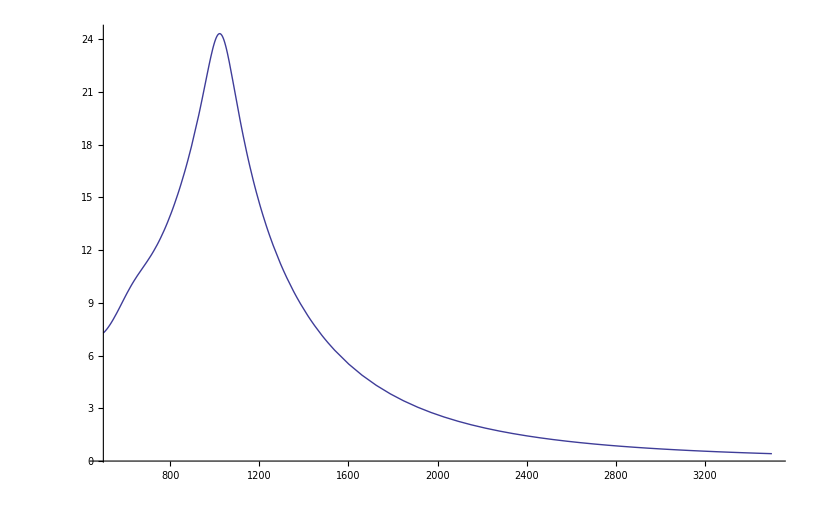

```mathematica
Plot[20*Log10[ftest]/.{f->1200},{f0,500,3500},PlotRange->All]
```

```mathematica
allZeros[[55]][[3]]*cM/(2*Pi)/.f0->1050
```

9070.1

```mathematica
1/(2*.87/1.2)
```

0.689655